```mathematica
SetDirectory["/home/leonard/Documents/ProjectData/PhysicalDistance/kickedRotorIDXP/k_2.0m_30_xp"];
```

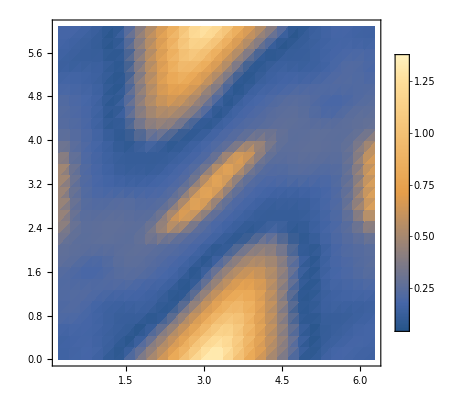

```mathematica
pos = Import["./pos.dat","Table"];
inds=Import["./inds.dat","Table"];
refs=Import["./refInds.dat","Table"];
posref={2.π-#[[1]],#[[2]]}&/@pos;
ListDensityPlot[Flatten/@Transpose[{posref,inds}],{PlotRange->All,PlotLegends->Automatic}]
```

```mathematica
Min[inds]
```

0.033361979274467983

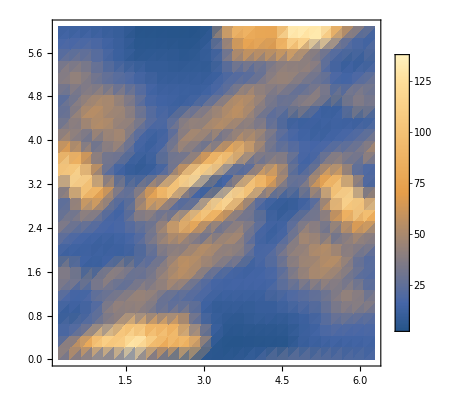

```mathematica
ListDensityPlot[Flatten/@Transpose[{posref,refs}],{PlotRange->All,PlotLegends->Automatic}]
```

```mathematica
klist = {0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,1.05,1.1,1.3,1.5,2.0,5.0};
kStr=If[FractionalPart[#]==0,ToString[#]<>"0",ToString[#]]&/@klist;
indList=Table[Import["/home/leonard/Documents/ProjectData/PhysicalDistance/kickedRotorIDXP/k_"<>k<>"m_30_xp/inds.dat","Table"],{k,kStr}];
Do[
fold="/home/leonard/Documents/ProjectData/PhysicalDistance/kickedRotorIDXP/k_"<>k<>"m_30_xp";
pos = Import[fold<>"/pos.dat","Table"];
inds=Import[fold<>"/inds.dat","Table"];
refs=Import[fold<>"/refInds.dat","Table"];
posref={2.π-#[[1]],#[[2]]}&/@pos;
Export["~/ph_"<>k<>".png",ListDensityPlot[Flatten/@Transpose[{posref,inds}],{PlotRange->All,PlotLegends->Automatic}]];
Export["~/ph_"<>k<>"_log.png",ListDensityPlot[Flatten/@Transpose[{posref,Log/@inds}],{PlotRange->All,PlotLegends->Automatic}]]
,{k,kStr}];
```

```mathematica
Do[
sampleSize=100;
trajLen=1000;
thetaMin=0.;
thetaMax=2.π;
pMin=0.;
pMax=2.π;
thLis={RandomReal[{thetaMin,thetaMax},{sampleSize}]};
pLis={RandomReal[{pMin,pMax},{sampleSize}]};
Do[
AppendTo[pLis,Mod[pLis[[-1]]+k*Sin[thLis[[-1]]],2.*π]];
AppendTo[thLis,Mod[thLis[[-1]]+pLis[[-1]],2.*π]];
,{trajLen}];
tb=Table[Transpose[{thLis[[;;,i]],pLis[[;;,i]]}],{i,1,sampleSize}];
Export["~/cl_"<>ToString[k]<>".png",ListPlot[tb[[;;,1;;500]],{PlotTheme->"Detailed",AspectRatio->1}]];
,{k,klist}];
```

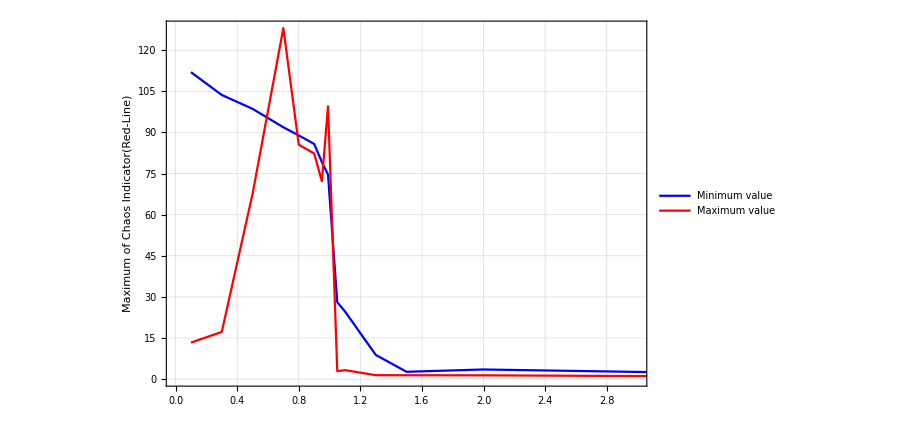

```mathematica
ListLinePlot[{Transpose[{klist,80*Min/@indList}],Transpose[{klist,Max/@indList}]},{PlotTheme->"Detailed",PlotStyle->{Blue,Red},FrameTicks->{{Automatic,{{0.,0.},{40,0.5},{80,1.},{120,1.5}}},{Automatic,None}},FrameLabel->{{"Maximum of Chaos Indicator(Red-Line)","Minimum of Chaos Indicaotr(Blue-Line)"},{None,None}},PlotLegends->Placed[{"Minimum value","Maximum value"},{Right,Center}]}]
```

```mathematica
kStr
```

{0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,1.05,1.1,1.3,1.5,2.0,5.0}

```mathematica
2.0
```

2.

```mathematica
FractionalPart[2.]
```

0.